```mathematica
MyShow[m_,g_]:=TableForm[{Graph[g,GraphLayout->"TutteEmbedding",ImageSize->150, VertexLabels->"Name"],
Graph[g,GraphLayout->"CircularEmbedding",ImageSize->150, VertexLabels->"Name"],Labeled[TraditionalForm[m],Style[TraditionalForm[FullSimplify[m[[1,1]]+m[[1,2]]]],Red,Bold]]},TableDirections->Row]
```

```mathematica
ContractGraph[g_,e_]:=Graph[VertexContract[gempty,{e[[1]],e[[2]]}],VertexLabels->{e[[1]]->{e}}]
```

```mathematica
gempty:=CycleGraph[5]
```

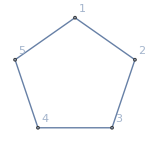
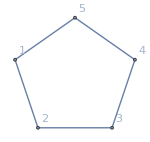
-Graphics- | -Graphics- | (α | λ-α
β | λ-β
γ | λ-γ
δ | λ-δ
ϵ | λ-ϵ)λ

```mathematica
empty:={{α,λ-α},{β,λ-β},{γ,λ-γ},{δ,λ-δ},{ϵ,λ-ϵ}};MyShow[empty,gempty]
```

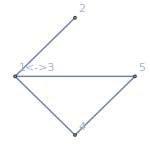
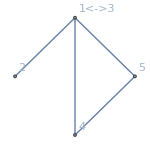
-Graphics- | -Graphics- | (α | 0
0 | α
γ2 | α-γ2
δ1 | α-δ1
0 | α)α

```mathematica
alfa:={{α,0},{0,α},{γ2,α-γ2},{δ1,α-δ1},{0,α}};MyShow[alfa,ContractGraph[gempty,1<->3]]
```

```mathematica
onethreecontract:=alfa;
```

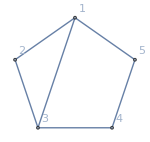
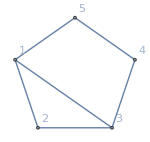
-Graphics- | -Graphics- | (0 | λ-α
β | -α-β+λ
γ-γ2 | -α-γ+γ2+λ
δ-δ1 | -α-δ+δ1+λ
ϵ | -α-ϵ+λ)λ-α

```mathematica
onethree:=empty-alfa;MyShow[onethree,EdgeAdd[gempty,1<->3]]
```

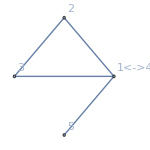
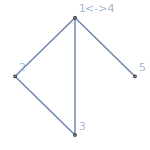
-Graphics- | -Graphics- | (0 | β
β | 0
0 | β
δ2 | β-δ2
ϵ1 | β-ϵ1)β

```mathematica
beta:={{0,β},{β,0},{0,β},{δ2,β-δ2},{ϵ1,β-ϵ1}};MyShow[beta,ContractGraph[gempty,1<->4]]
```

```mathematica
onefourcontract:=beta;
```

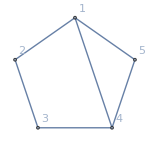
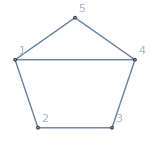
-Graphics- | -Graphics- | (α | -α-β+λ
0 | λ-β
γ | -β-γ+λ
δ-δ2 | -β-δ+δ2+λ
ϵ-ϵ1 | -β-ϵ+ϵ1+λ)λ-β

```mathematica
onefour:=empty-beta;MyShow[onefour,EdgeAdd[gempty,1<->4]]
```

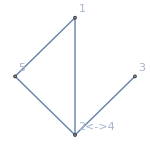
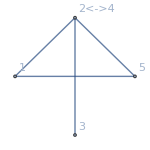
-Graphics- | -Graphics- | (α1 | γ-α1
0 | γ
γ | 0
0 | γ
ϵ2 | γ-ϵ2)γ

```mathematica
gamma:={{α1,γ-α1},{0,γ},{γ,0},{0,γ},{ϵ2,γ-ϵ2}};MyShow[gamma,ContractGraph[gempty,2<->4]]
```

```mathematica
twofourcontract:=gamma;
```

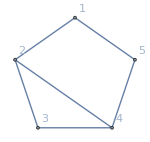
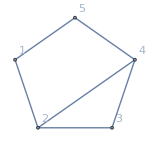
-Graphics- | -Graphics- | (α-α1 | -α+α1-γ+λ
β | -β-γ+λ
0 | λ-γ
δ | -γ-δ+λ
ϵ-ϵ2 | -γ-ϵ+ϵ2+λ)λ-γ

```mathematica
twofour:=empty-gamma;MyShow[twofour,EdgeAdd[gempty,2<->4]]
```

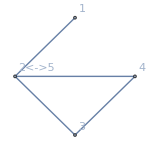
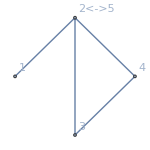
-Graphics- | -Graphics- | (α2 | δ-α2
β1 | δ-β1
0 | δ
δ | 0
0 | δ)δ

```mathematica
delta:={{α2,δ-α2},{β1,δ-β1},{0,δ},{δ,0},{0,δ}};MyShow[delta,ContractGraph[gempty,2<->5]]
```

```mathematica
twofivecontract:=delta;
```

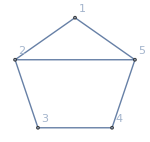
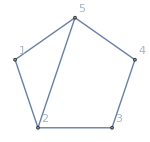
-Graphics- | -Graphics- | (α-α2 | -α+α2-δ+λ
β-β1 | -β+β1-δ+λ
γ | -γ-δ+λ
0 | λ-δ
ϵ | -δ-ϵ+λ)λ-δ

```mathematica
twofive:=empty-delta;MyShow[twofive,EdgeAdd[gempty,2<->5]]
```

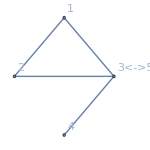
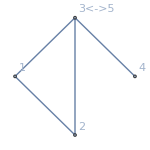
-Graphics- | -Graphics- | (0 | ϵ
β2 | ϵ-β2
γ1 | ϵ-γ1
0 | ϵ
ϵ | 0)ϵ

```mathematica
epsilon:={{0,ϵ},{β2,ϵ-β2},{γ1,ϵ-γ1},{0,ϵ},{ϵ,0}};MyShow[epsilon,ContractGraph[gempty,3<->5]]
```

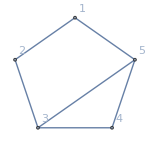
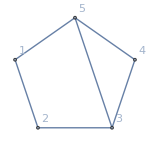
-Graphics- | -Graphics- | (α | -α-ϵ+λ
β-β2 | -β+β2-ϵ+λ
γ-γ1 | -γ+γ1-ϵ+λ
δ | -δ-ϵ+λ
0 | λ-ϵ)λ-ϵ

```mathematica
threefive:=empty-epsilon;MyShow[threefive,EdgeAdd[gempty,3<->5]]
```

```mathematica
threefivecontract:=epsilon;
```

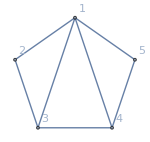
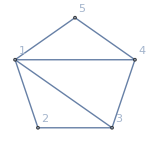
-Graphics- | -Graphics- | (0 | -α-β+λ
0 | -α-β+λ
γ-γ2 | -α-β-γ+γ2+λ
δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ)-α-β+λ

```mathematica
oneamigo1:=onethree-onefourcontract;MyShow[oneamigo1,EdgeAdd[gempty,{1<->3,1<->4}]]
```

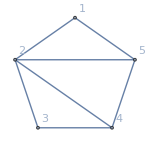
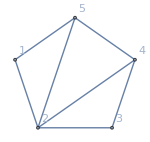
-Graphics- | -Graphics- | (α-α1-α2 | -α+α1+α2-γ-δ+λ
β-β1 | -β+β1-γ-δ+λ
0 | -γ-δ+λ
0 | -γ-δ+λ
ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ)-γ-δ+λ

```mathematica
oneamigo2:=twofive-twofourcontract;MyShow[oneamigo2,EdgeAdd[gempty,{2<->5,2<->4}]]
```

```mathematica
oneamigo3:=threefive;
```

```mathematica
twoamigo1:=twofive-twofourcontract;MyShow[twoamigo1,EdgeAdd[gempty,{2<->5,2<->4}]]
```

-Graphics- | -Graphics- | (α-α1-α2 | -α+α1+α2-γ-δ+λ
β-β1 | -β+β1-γ-δ+λ
0 | -γ-δ+λ
0 | -γ-δ+λ
ϵ-ϵ2 | -γ-δ-ϵ+ϵ2+λ)-γ-δ+λ

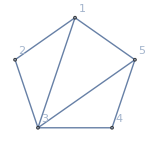
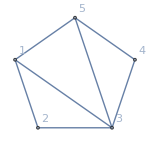
-Graphics- | -Graphics- | (0 | -α-ϵ+λ
β-β2 | -α-β+β2-ϵ+λ
γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
δ-δ1 | -α-δ+δ1-ϵ+λ
0 | -α-ϵ+λ)-α+λ-ϵ

```mathematica
twoamigo2:=onethree-threefivecontract;MyShow[twoamigo2,EdgeAdd[gempty,{3<->5,3<->1}]]
```

```mathematica
twoamigo3:=onefour;
```

```mathematica
threeamigo1:=onethree-threefivecontract;MyShow[threeamigo1,EdgeAdd[gempty,{3<->5,3<->1}]]
```

-Graphics- | -Graphics- | (0 | -α-ϵ+λ
β-β2 | -α-β+β2-ϵ+λ
γ-γ1-γ2 | -α-γ+γ1+γ2-ϵ+λ
δ-δ1 | -α-δ+δ1-ϵ+λ
0 | -α-ϵ+λ)-α+λ-ϵ

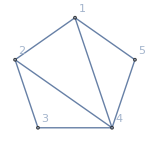
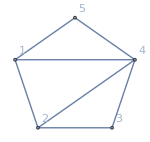
-Graphics- | -Graphics- | (α-α1 | -α+α1-β-γ+λ
0 | -β-γ+λ
0 | -β-γ+λ
δ-δ2 | -β-γ-δ+δ2+λ
ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ)-β-γ+λ

```mathematica
threeamigo2:=onefour-twofourcontract;MyShow[threeamigo2,EdgeAdd[gempty,{4<->1,4<->2}]]
```

```mathematica
threeamigo3:=twofive;
```

```mathematica
fouramigo1:=onefour-twofourcontract;MyShow[fouramigo1,EdgeAdd[gempty,{4<->1,4<->2}]]
```

-Graphics- | -Graphics- | (α-α1 | -α+α1-β-γ+λ
0 | -β-γ+λ
0 | -β-γ+λ
δ-δ2 | -β-γ-δ+δ2+λ
ϵ-ϵ1-ϵ2 | -β-γ-ϵ+ϵ1+ϵ2+λ)-β-γ+λ

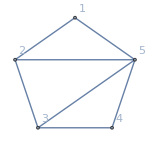
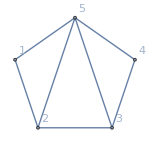
-Graphics- | -Graphics- | (α-α2 | -α+α2-δ-ϵ+λ
β-β1-β2 | -β+β1+β2-δ-ϵ+λ
γ-γ1 | -γ+γ1-δ-ϵ+λ
0 | -δ-ϵ+λ
0 | -δ-ϵ+λ)-δ+λ-ϵ

```mathematica
fouramigo2:=twofive-threefivecontract;MyShow[fouramigo2,EdgeAdd[gempty,{5<->2,5<->3}]]
```

```mathematica
fouramigo3:=onethree;
```

```mathematica
fiveamigo1:=twofive-threefivecontract;MyShow[fiveamigo1,EdgeAdd[gempty,{5<->2,5<->3}]]
```

-Graphics- | -Graphics- | (α-α2 | -α+α2-δ-ϵ+λ
β-β1-β2 | -β+β1+β2-δ-ϵ+λ
γ-γ1 | -γ+γ1-δ-ϵ+λ
0 | -δ-ϵ+λ
0 | -δ-ϵ+λ)-δ+λ-ϵ

```mathematica
fiveamigo2:=onethree-onefourcontract;MyShow[fiveamigo2,EdgeAdd[gempty,{1<->3,1<->4}]]
```

-Graphics- | -Graphics- | (0 | -α-β+λ
0 | -α-β+λ
γ-γ2 | -α-β-γ+γ2+λ
δ-δ1-δ2 | -α-β-δ+δ1+δ2+λ
ϵ-ϵ1 | -α-β-ϵ+ϵ1+λ)-α-β+λ

```mathematica
fiveamigo3:=twofour;
```

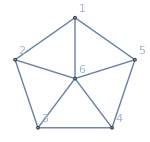
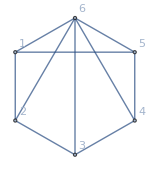
-Graphics- | -Graphics- | (α1+α2 | α-α1-α2+β+γ+δ+ϵ-λ
β1+β2 | α+β-β1-β2+γ+δ+ϵ-λ
γ1+γ2 | α+β+γ-γ1-γ2+δ+ϵ-λ
δ1+δ2 | α+β+γ+δ-δ1-δ2+ϵ-λ
ϵ1+ϵ2 | α+β+γ+δ+ϵ-ϵ1-ϵ2-λ)α+β+γ+δ-λ+ϵ

```mathematica
full:=2*empty-( oneamigo1+oneamigo2+oneamigo3)//FullSimplify;MyShow[full,EdgeAdd[gempty,Table[i<->6,{i,5}]]]
```

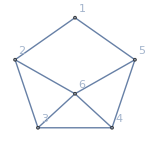
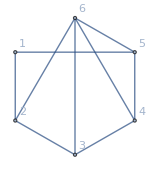
-Graphics- | -Graphics- | (α1+α2 | -α1-α2+γ+δ+ϵ
β1+β2 | -β1-β2+γ+δ+ϵ
γ+γ1 | -γ1+δ+ϵ
δ | γ+ϵ
ϵ+ϵ2 | γ+δ-ϵ2)γ+δ+ϵ

```mathematica
onegone:=full+oneamigo1//FullSimplify;MyShow[onegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4,5}}]]]
```

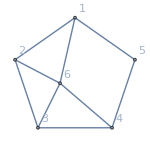
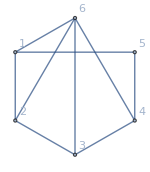
-Graphics- | -Graphics- | (α+α1 | -α1+β+γ
β | α+γ
γ+γ2 | α+β-γ2
δ1+δ2 | α+β+γ-δ1-δ2
ϵ1+ϵ2 | α+β+γ-ϵ1-ϵ2)α+β+γ

```mathematica
fivegone:=full+fiveamigo1//FullSimplify;MyShow[fivegone,EdgeAdd[gempty,Table[i<->6,{i,{1,2,3,4}}]]]
```

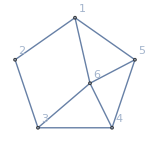
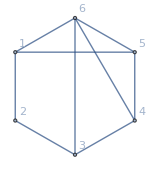
-Graphics- | -Graphics- | (α | β+ϵ
β+β2 | α-β2+ϵ
γ1+γ2 | α+β-γ1-γ2+ϵ
δ1+δ2 | α+β-δ1-δ2+ϵ
ϵ+ϵ1 | α+β-ϵ1)α+β+ϵ

```mathematica
twogone:=full+twoamigo1//FullSimplify;MyShow[twogone,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

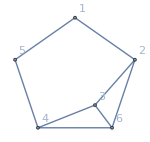
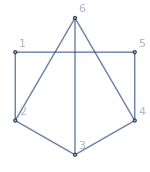
-Graphics- | -Graphics- | (α+α1 | -α-α1+γ+λ
β | -β+γ+λ
2 γ | λ-γ
δ | γ-δ+λ
ϵ+ϵ2 | γ-ϵ-ϵ2+λ)γ+λ

```mathematica
onefivegone:=full+fiveamigo1+oneamigo1//FullSimplify;MyShow[onefivegone,EdgeAdd[gempty,Table[i<->6,{i,{2,3,4}}]]]
```

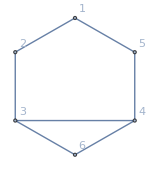
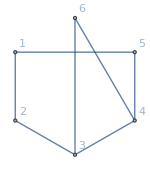
-Graphics- | -Graphics- | (α+α1+α2 | -α-α1-α2+γ+δ+λ
β+β1 | -β-β1+γ+δ+λ
2 γ | -γ+δ+λ
2 δ | γ-δ+λ
ϵ+ϵ2 | γ+δ-ϵ-ϵ2+λ)γ+δ+λ

```mathematica
onetwofivegone:=onefivegone+delta//FullSimplify;MyShow[onetwofivegone,EdgeAdd[gempty,Table[i<->6,{i,{3,4}}]]]
```

```mathematica
withoutspike1:=full+oneamigo1//FullSimplify;MyShow[withoutspike1,EdgeAdd[gempty,Table[i<->6,{i,2,5}]]]
```

-Graphics- | -Graphics- | (α1+α2 | -α1-α2+γ+δ+ϵ
β1+β2 | -β1-β2+γ+δ+ϵ
γ+γ1 | -γ1+δ+ϵ
δ | γ+ϵ
ϵ+ϵ2 | γ+δ-ϵ2)γ+δ+ϵ

```mathematica
withoutspike2:=full+oneamigo2//FullSimplify;MyShow[withoutspike2,EdgeAdd[gempty,Table[i<->6,{i,{1,3,4,5}}]]]
```

-Graphics- | -Graphics- | (α | β+ϵ
β+β2 | α-β2+ϵ
γ1+γ2 | α+β-γ1-γ2+ϵ
δ1+δ2 | α+β-δ1-δ2+ϵ
ϵ+ϵ1 | α+β-ϵ1)α+β+ϵ

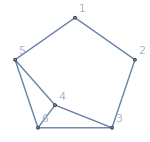
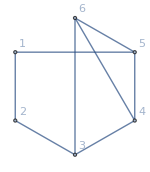
-Graphics- | -Graphics- | (α | -α+ϵ+λ
β+β2 | -β-β2+ϵ+λ
γ+γ1 | -γ-γ1+ϵ+λ
δ | -δ+ϵ+λ
2 ϵ | λ-ϵ)λ+ϵ

```mathematica
without2spikes1:=withoutspike1+oneamigo2//FullSimplify;MyShow[without2spikes1,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

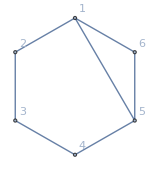
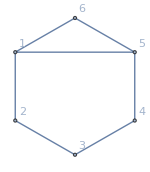
-Graphics- | -Graphics- | (2 α | -2 α+ϵ+2 λ
2 β+β2 | -2 β-β2+ϵ+2 λ
2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2 δ | -2 δ+ϵ+2 λ
3 ϵ | 2 λ-2 ϵ)2 λ+ϵ

```mathematica
without3spikes1:=without2spikes1+empty//FullSimplify;MyShow[without3spikes1,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

```mathematica
without2spikes2:=withoutspike2+oneamigo1//FullSimplify;MyShow[without2spikes2,EdgeAdd[gempty,Table[i<->6,{i,{3,4,5}}]]]
```

-Graphics- | -Graphics- | (α | -α+ϵ+λ
β+β2 | -β-β2+ϵ+λ
γ+γ1 | -γ-γ1+ϵ+λ
δ | -δ+ϵ+λ
2 ϵ | λ-ϵ)λ+ϵ

```mathematica
without3spikes2:=without2spikes2+empty//FullSimplify;MyShow[without3spikes2,EdgeAdd[gempty,Table[i<->6,{i,{1,5}}]]]
```

-Graphics- | -Graphics- | (2 α | -2 α+ϵ+2 λ
2 β+β2 | -2 β-β2+ϵ+2 λ
2 γ+γ1 | -2 γ-γ1+ϵ+2 λ
2 δ | -2 δ+ϵ+2 λ
3 ϵ | 2 λ-2 ϵ)2 λ+ϵ

```mathematica
Assuming[
{α>0,β>0,γ>0,δ>0,ϵ>0,α1>=0,α2>=0,β1>=0,β2>=0,γ1>=0,γ2>=0,δ1>=0,δ2>=0,ϵ1>=0,ϵ>=0},
Solve[2*empty-( oneamigo1+oneamigo2+oneamigo3)=={{0,0},{0,0},{0,0},{0,0},{0,0}}]
]
```

{{α2→-α1,β2→-β1,γ2→-γ1,δ2→-δ1,ϵ2→-ϵ1,λ→α+β+γ+δ+ϵ}}